```mathematica
incidenceToTransmissionAngle[n1_, n2_, θ_] := ArcSin[n1/n2 Sin[θ]]
transferMatrixS[n1_, n2_, θ_] := Module[{
θt = incidenceToTransmissionAngle[n1, n2, θ],
r, t
},
r = (n1 Cos[θ] - n2 Cos[θt]) / (n1 Cos[θ] + n2 Cos[θt]);
t = 2 n1 Cos[θ] / (n1 Cos[θ] + n2 Cos[θt]);
{{1, r}, {r, 1}} / t
]
propogationMatrix[n_, d_, λ_, θ_] := Module[{
ϕ = 2 Pi n d Cos[θ] / λ
},
{{E^(-I ϕ), 0}, {0, E^(I ϕ)}}
]
quarterThickness[n_, λ_] := λ / (4 n)
interactionMatrixS[media_, λ_, θ_] := 
If[Length[media] > 2,
Dot@@MovingMap[
transferMatrixS[Lookup[#1[[1]], n], Lookup[#1[[2]], n], θ] .
 propogationMatrix[Lookup[#1[[2]], n], Lookup[#1[[2]], d], λ, θ] &,
media[[1;;-2]], 1
],
IdentityMatrix[2]
] .
transferMatrixS[media[[-2]][n], media[[-1]][n], θ]
reflectionS[media_, λ_, θ_] := (Abs[#[[2]]/#[[1]]]^2 &)[interactionMatrixS[media, λ, θ] . {1, 0}]
```

{<|n→1.,d→1.7×10^-7|>,<|n→1.3,d→1.31×10^-7|>,<|n→1.7,d→1.×10^-7|>,<|n→1.85,d→9.2×10^-8|>,<|n→2.05,d→8.3×10^-8|>,<|n→2.3,d→7.4×10^-8|>,<|n→2.55,d→6.7×10^-8|>,<|n→2.8,d→6.1×10^-8|>}

0.0106351

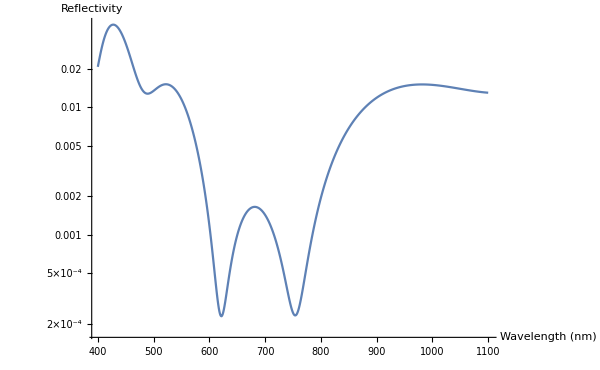

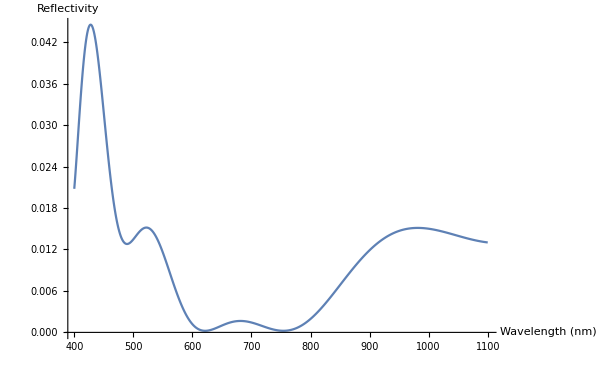

```mathematica
mediaIndicies = Round[{1.0, 1.3, Sequence@@ReleaseHold[Hold[Table[1.69^((n - k)/n) 2.8^(k/n), {k, 0, n}]] /. n -> 5]}, 0.05];
media = <|n -> #1, d -> N@Round[quarterThickness[#1, 680 10^-9], 10^-9]|> & /@ mediaIndicies
data = ParallelTable[{a 10^9, reflectionS[media, a, 0]}, {a, 400 10^-9, 1100 10^-9, 10^-9}];
Integrate[Interpolation[data][λ], {λ, 400, 1100}]/(1100 - 400)
ListLogPlot[data, Joined->True, PlotRange->All, AxesLabel->{"Wavelength (nm)", "Reflectivity"}, ImageSize->600]
ListPlot[data, Joined->True, PlotRange->All, AxesLabel->{"Wavelength (nm)", "Reflectivity"}, ImageSize->600]
```